```mathematica
path="/Users/wiese/fBm-simulations/";
<<"/Users/wiese/Mathematica/libraries/Kay-initialization.m"
export=True;
```

```mathematica
If[choice=!=1,choice=1,choice=3];
Print["choice = ",choice]
Which[choice==1,
NN=2^24;HH=0.45,
choice==2,
NN=2^18;HH=0.45;
choice==3,
NN=2^24;HH=0.55,
];
```

choice = 3

```mathematica
filepattern=path<>"fBm_HistoXT(H="<>ToString[HH]<>",T="<>ToString[NN]<>",seed=*).dat";
If[verbatim>1,Print["Import : ",filepattern,", N = 2^",FS[Log[NN]/Log[2]]]];
filenames=FileNames[filepattern];
For[i=1; data=0; seeds={},i≤Length[filenames],i++,
data+=(data5=Import[filenames[[i]],"CSV"]);
(* get the seed *)
	X=filenames[[i]];
Print[X];
	where=StringPosition[X,"seed="]//Flatten;
	X=StringDrop[X,where[[2]]];
	where=StringPosition[X,").dat"]//Flatten;
	X=StringTake[X,where[[1]]-1];seed=X//ToExpression;
	seeds=Union[seeds,{seed}];
Print["seed ",seed," has ",data5[[5]]//Total," data points." ];
];
Print["seeds are ",seeds]
data[[5]]//Total
```

/Users/wiese/fBm-simulations/fBm_HistoXT(H=0.55,T=16777216,seed=20).dat

seed 20 has 40901 data points.

/Users/wiese/fBm-simulations/fBm_HistoXT(H=0.55,T=16777216,seed=2).dat

seed 2 has 25101 data points.

/Users/wiese/fBm-simulations/fBm_HistoXT(H=0.55,T=16777216,seed=3).dat

seed 3 has 15601 data points.

/Users/wiese/fBm-simulations/fBm_HistoXT(H=0.55,T=16777216,seed=5).dat

seed 5 has 308201 data points.

seeds are {2,3,5,20}

389804

```mathematica
(* 21.9.2017: H=0.45 : 95172 data points, H=0.55 : 67543 data points *)
(* 25.9.2017: H=0.45 : 102591 data points, H=0.55 : 67543 data points *)
(* 27.9.2017: H=0.45 : 102591 data points, H=0.55 : 71430 data points *)
moreonly=True;
filepattern=path<>"fBm_histoExpTabs(H="<>ToString[HH]<>",T="<>ToString[NN]<>",seed=*).dat";
If[verbatim>1,Print["Import : ",filepattern,", N = 2^",FS[Log[NN]/Log[2]]]];
filenames=FileNames[filepattern];
For[i=1; dataExpT=0;dataExpT2=0; seeds={};totalsamples=0,i≤Length[filenames],i++,
(* get the number of data points from another file *)
filename2=StringDrop[filenames[[i]],StringLength[path]+StringLength["fBm_histoExpTabs"]];
filename2=path<>"fBm_X0_Histo"<>filename2;
filename3=StringDrop[filenames[[i]],StringLength[path]+StringLength["fBm_histoExpTabs"]];
filename3=path<>"fBm_histoExpTabs2"<>filename3;
samples=Import[filename2,"CSV"]//Flatten//Total;
totalsamples+=samples;
dataExpT+=(Import[filenames[[i]],"CSV"]//Flatten)*samples;
dataExpT2+=(Import[filename3,"CSV"]//Flatten)*samples;
(* get the seed *)
	XX=X=filenames[[i]];
	where=StringPosition[X,"seed="]//Flatten;
	X=StringDrop[X,where[[2]]];
	where=StringPosition[X,").dat"]//Flatten;
	X=StringTake[X,where[[1]]-1];seed=X//ToExpression;
	seeds=Union[seeds,{seed}];
If[(!moreonly) || samples-oldsamples[HH,seed]>0,Print[XX];Print["seed ",seed," has ",samples," data points, i.e. " ,samples-oldsamples[HH,seed]," more."]];
oldsamples[HH,seed]=samples;
];
Print["total samples = ",totalsamples];
Print[totalsamples-oldsamples[HH]," more data points since last update on ",olddate[HH]];
oldsamples[HH]=totalsamples;
olddate[HH]=DateString[];
dataExpT=dataExpT/totalsamples;
dataExpT2=dataExpT2/totalsamples;
Print["seeds are ",seeds]
```

/Users/wiese/fBm-simulations/fBm_histoExpTabs(H=0.55,T=16777216,seed=2127).dat

seed 2127 has 3991 data points, i.e. 700 more.

/Users/wiese/fBm-simulations/fBm_histoExpTabs(H=0.55,T=16777216,seed=2129).dat

seed 2129 has 3991 data points, i.e. 350 more.

/Users/wiese/fBm-simulations/fBm_histoExpTabs(H=0.55,T=16777216,seed=2139).dat

seed 2139 has 3990 data points, i.e. 900 more.

/Users/wiese/fBm-simulations/fBm_histoExpTabs(H=0.55,T=16777216,seed=2140).dat

seed 2140 has 3991 data points, i.e. 130 more.

/Users/wiese/fBm-simulations/fBm_histoExpTabs(H=0.55,T=16777216,seed=2141).dat

seed 2141 has 3991 data points, i.e. 1730 more.

/Users/wiese/fBm-simulations/fBm_histoExpTabs(H=0.55,T=16777216,seed=2144).dat

seed 2144 has 3990 data points, i.e. 10 more.

total samples = 2187030

3820 more data points since last update on Mon 26 Feb 2018 11:39:34

seeds are {6,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,1385,1386,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2105,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2145,20004,20005}

```mathematica
Print["samples = ",oldsamples[0.45]," for H=0.45, and ",oldsamples[0.55]," for H=0.55."]
```

samples = 1640097 for H=0.45, and 2187030 for H=0.55.

```mathematica
data2=data;
coarsen=5;
X=For[i=1,i≤ Length[data2],i+=coarsen,
X=data2[[i]];
For[j=1,j<coarsen,j++,If[i+j≤ Length[data2], X+=data2[[i+j]]];];
Sow[X]
]//Reap;
data2=X[[2,1]];

data2=data2//Transpose;

X=For[i=1,i≤ Length[data2],i+=coarsen,
X=data2[[i]];
For[j=1,j<coarsen,j++,If[i+j≤ Length[data2], X+=data2[[i+j]]];];
Sow[X]
]//Reap;
data2=X[[2,1]];
data2=data2//Transpose;
```

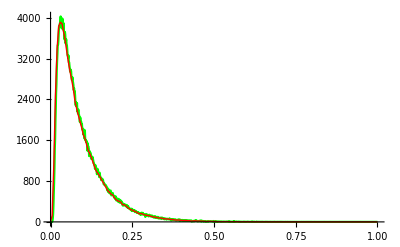

```mathematica
xtab1=Table[i/1000,{i,0,1000}];xtab2=Table[i/1000,{i,0,1000,coarsen}];
{ListLinePlot[Transpose[{xtab1,data[[500]]}],PlotStyle->Green,PlotRange->All],ListLinePlot[Transpose[{xtab2,data2[[500/coarsen//Round]]/coarsen^2}],PlotStyle->{Thick,Red},PlotRange->All]}//Show
```

```mathematica
(* ListPlot3D[data2/coarsen^2,PlotRange->{{0,250/coarsen//Round},{0,1000/coarsen//Round},{0,2000}},AxesLabel->{t,x,P}] *)
```

```mathematica
(* show <T(x)> *)
```

```mathematica
oneloopT=1/((-1+x) x)4 (-x^2+Log[2 π]+x ((-1+x) Log[1-x]+x Log[x])-PolyGamma[-2,1-x]-PolyGamma[-2,1+x]);
norm=NIntegrate[(x(1-x))^(1/HH-1)Exp[oneloopT (HH-1)],{x,0,1}]/Integrate[x(1-x),{x,0,1}]
oneloopThalf=oneloopT/.x->1/2.
```

0.776977

1.47084

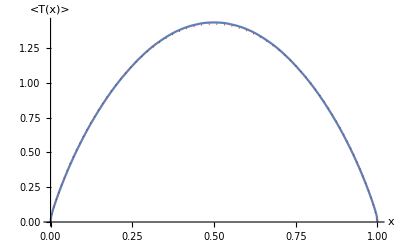

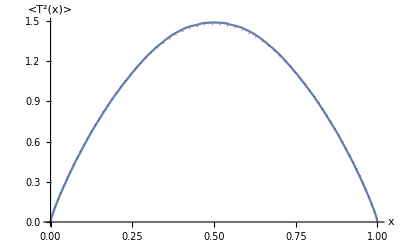

```mathematica
(* the histogram data *)
α=1/HH-1;
Texp=Range[1,1001]-1;
T2exp=Range[1,1001]-1;
For[i=1,i<1001,i++,
Texp[[i]]=data[[i]].Range[0,1000];
T2exp[[i]]=data[[i]].(Range[0,1000]^2);
]
(Texp+Reverse[Texp])/2;
Texp=%/Mean[Texp];
(T2exp+Reverse[T2exp])/2;
T2exp=%/Mean[T2exp];
ListLinePlot[dataT=Transpose[{xtab1,Texp}]];
Plot[(x(1-x))^α/(Gamma[1+α]^2/Gamma[2+2 α]),{x,0,1},PlotStyle->{Dotted,Thick,Red}];
Show[%%,%,AxesLabel->{x,"<T(x)>"}]
ListLinePlot[dataT2=Transpose[{xtab1,T2exp}]];
T2int=NIntegrate[((-1+x) x (-1-x+x^2))^α,{x,0,1}];
Plot[((-1+x) x (-1-x+x^2))^α/T2int,{x,0,1},PlotStyle->{Dotted,Thick,Red}];
Show[%%%,%,AxesLabel->{x,"<T^2(x)>"}]
```

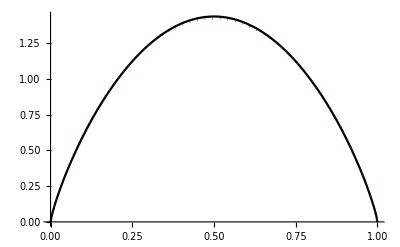

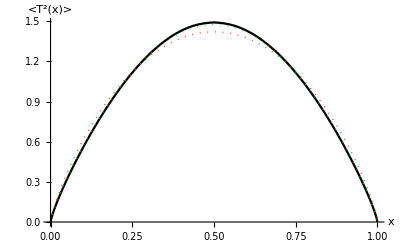

```mathematica
(* the measured first moment of T *)
α=1/HH-1;
(dataExpT+Reverse[dataExpT])/2;
dataExpTsym=%/Mean[dataExpT];
ListLinePlot[dataTv2=Transpose[{xtab1,dataExpTsym}],PlotStyle->Black];
Plot[(x(1-x))^α/(Gamma[1+α]^2/Gamma[2+2 α]),{x,0,1},PlotStyle->{Dotted,Thick,Red}];
Show[%%,%]
(* the measured second moments of T *)
(dataExpT2+Reverse[dataExpT2])/2;
dataExpT2sym=%/Mean[dataExpT2];
ListLinePlot[dataT2v2=Transpose[{xtab1,dataExpT2sym}],PlotStyle->Black];
NIntegrate[(-(-1+x) x )^α,{x,0,1}];
Plot[(-(-1+x) x )^α/%,{x,0,1},PlotStyle->{Dotted,Thick,Red}];
NIntegrate[((-1+x) x /12(-1-x+x^2))^α,{x,0,1}];
Plot[((-1+x) x /12(-1-x+x^2))^α/%,{x,0,1},PlotStyle->{Dotted,Thick,Green}];
Show[%%%%%,%%%,%,AxesLabel->{x,"<T^2(x)>"}]
```

```mathematica
(* check <T(X)> *)
```

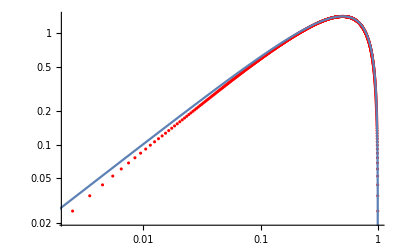

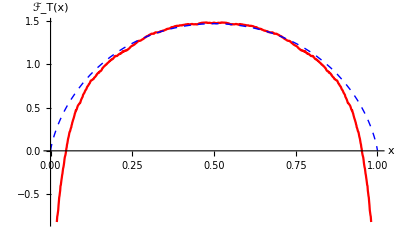

```mathematica
(* this is constructed from the distribution *)
α=1/HH-1;
todrop=2;
Texp;
(%+Reverse[%])/2;
Transpose[{xtab1,%}];
Drop[%,todrop];
Drop[%,-todrop];
inter=%/.{a_,b_}->{(a-1/2)0.999+0.5,b-0.015};
{ListLogLogPlot[inter,PlotStyle->Red],LogLogPlot[(x(1-x))^α/(Gamma[1+α]^2/Gamma[2+2 α]),{x,0.0001,1}]}//Show
%%/.{a_,b_}->{a,b/(a(1-a))^((1/HH-1))};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
Drop[Drop[Transpose[%][[2]],400],-400]//Mean;
%%/.{a_,b_}->{a,b-%+oneloopThalf};
ListLinePlot[%,PlotStyle->Red];
Plot[((oneloopT)),{x,0,1},PlotStyle->{Thick,Blue,Dashed}];
Show[%%,%,PlotRange->All,AxesLabel->{x,Subscript[ℱ, T][x]}]
```

2187030

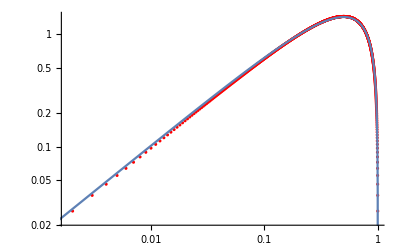

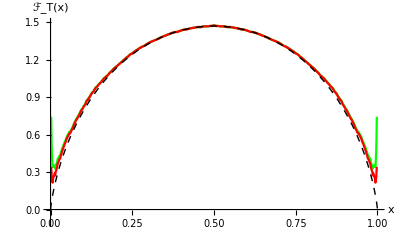

/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT-H=0p55.eps

```mathematica
(* this is the measured expectation of Subscript[T, abs](x) *)
(* red = corrected, green = original data *)
α=1/HH-1;
todrop=2;
totalsamples
dataTv2;
Drop[%,todrop];
inter=Drop[%,-todrop];
If[HH==0.45,inter2=%/.{a_,b_}->{(a-1/2)0.999+1/2,b},inter2=%/.{a_,b_}->{(a-1/2)0.9999+1/2,b}];
{ListLogLogPlot[inter2,PlotStyle->Red],LogLogPlot[(x(1-x))^α/(Gamma[1+α]^2/Gamma[2+2 α]),{x,0.0001,1}]}//Show
inter/.{a_,b_}->{a,b/(a(1-a))^((1/HH-1))};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
Drop[Drop[Transpose[%][[2]],470],-470]//Mean;
FTdata[HH]=%%/.{a_,b_}->{a,b-%+oneloopThalf};
P8=ListLinePlot[%,PlotStyle->Green];

inter2/.{a_,b_}->{a,b/(a(1-a))^((1/HH-1))};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
Drop[Drop[Transpose[%][[2]],470],-470]//Mean;
FTdata2[HH]=%%/.{a_,b_}->{a,b-%+oneloopThalf};
P9=ListLinePlot[%,PlotStyle->Red];

Plot[((oneloopT)),{x,0,1},PlotStyle->{Thick,Black,Dashed}];
FT[HH]=Show[P8,P9,%,PlotRange->{-0.1,1.5},AxesLabel->{x,Subscript[ℱ, T][x]}]
If[export,Export["/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT-H="<>StringReplace[ToString[HH],"."->"p"]<>".eps",%]]
```

```mathematica
(* <T^2(x)> attention: NOW hopfeully (approximately) correct SCALING FUNCTION *)
```

```mathematica
fitT2=1.2672243979366526-3.6204667873036875 (-1/2+x)^2-24.174130256028786 (-1/2+x)^4+1169.5396070693405 (-1/2+x)^6-33037.2577657247 (-1/2+x)^8+529945.4658897913 (-1/2+x)^10-5.149081400487961*^6 (-1/2+x)^12+3.0837219209621537*^7 (-1/2+x)^14-1.1122808520954467*^8 (-1/2+x)^16+2.2146558579021466*^8 (-1/2+x)^18-1.869308785283066*^8 (-1/2+x)^20;
```

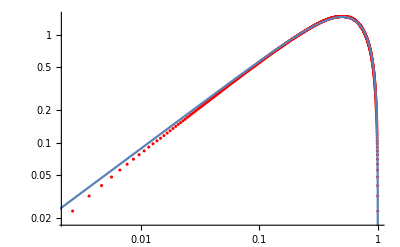

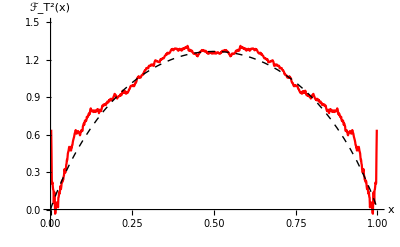

```mathematica
(* this is constructed from the distribution; *)
α=1/HH-1;
todrop=2;
T2exp;
(%+Reverse[%])/2;
Transpose[{xtab1,%}];
Drop[%,todrop];
Drop[%,-todrop];
inter=%;
inter2=%/.{a_,b_}->{(a-1/2)0.9987+1/2,b};
T2int=NIntegrate[((-1+x) x/12 (-1-x+x^2))^α,{x,0,1}];
{ListLogLogPlot[inter2,PlotStyle->Red],LogLogPlot[((-1+x) x /12(-1-x+x^2))^α/T2int,{x,0.0001,1}]};
%//Show
inter/.{x_,b_}->{x,b/(((-1+x) x (-1-x+x^2))^α/T2int)};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
Drop[Drop[Transpose[%][[2]],400],-400]//Mean;
%%/.{a_,b_}->{a,b-%+1.2672243979366526};
ListLinePlot[%,PlotStyle->Red];
(* now hopefully correct theory curve *)
Plot[fitT2,{x,0,1},PlotStyle->{Thick,Black,Dashed}];
Show[%%,%,PlotRange->{-.1,1.5},AxesLabel->{x,Subscript[ℱ, T^2][x]}]
```

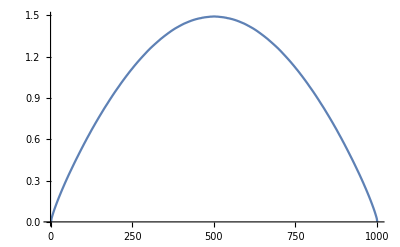

```mathematica
dataExpT2sym//ListLinePlot
```

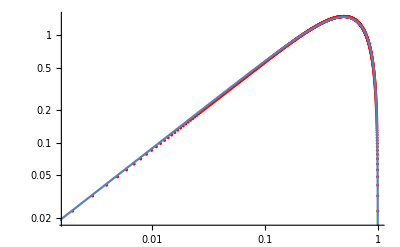

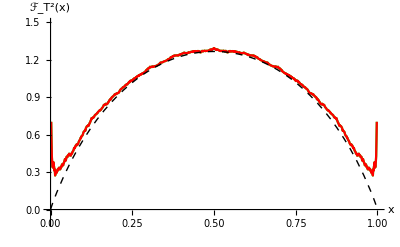

/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT2-H=0p55.eps

```mathematica
(* attention: corrected SCALING FUNCTION *)
(* red = corrected *)
α=1/HH-1;
todrop=2;
dataExpT2sym;
Transpose[{xtab1,%}];
Drop[%,todrop];
inter=Drop[%,-todrop];
If[HH==0.45,inter2=%/.{a_,b_}->{(a-1/2)0.9985+1/2,b},inter2=%/.{a_,b_}->{(a-1/2)1.000+1/2,b}];
T2int=NIntegrate[((-1+x) x/12 (-1-x+x^2))^α,{x,0,1}];
P11={ListLogLogPlot[inter2,PlotStyle->Red],LogLogPlot[((-1+x) x /12(-1-x+x^2))^α/T2int,{x,0.0001,1}]}//Show
inter/.{x_,b_}->{x,b/(1/12(((1-x) x) (1+x-x^2))^α/T2int)};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
%/.{a_,b_}->{a,b};
Drop[Drop[Transpose[%][[2]],400],-400]//Mean;
FT2data[HH]=%%/.{a_,b_}->{a,b-%+(fitT2/.x->1/2)};
P12=ListLinePlot[%,PlotStyle->Green,PlotRange->All];
inter2/.{x_,b_}->{x,b/(1/12(((1-x) x) (1+x-x^2))^α/T2int)};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
%/.{a_,b_}->{a,b};
Drop[Drop[Transpose[%][[2]],400],-400]//Mean;
FT2data2[HH]=%%/.{a_,b_}->{a,b-%+(fitT2/.x->1/2)};
P13=ListLinePlot[%,PlotStyle->Red,PlotRange->All];
Plot[fitT2,{x,0,1},PlotStyle->{Thick,Black,Dashed}];
FT2[HH]=Show[P12,P13,%,PlotRange->{-.1,1.5},AxesLabel->{x,Subscript[ℱ, T^2][x]}]
If[export,Export["/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT2-H="<>StringReplace[ToString[HH],"."->"p"]<>".eps",%]]
```

```mathematica
dataExpT/Mean[dataExpT];
Transpose[{xtab1,%}];
Drop[%,todrop];
inter=Drop[%,-todrop];
If[HH==0.45,inter2=%/.{a_,b_}->{(a-1/2)0.9985+1/2,b},inter2=%/.{a_,b_}->{(a-1/2)1.000+1/2,b}];
Tint=NIntegrate[((-1+x) x/12 )^α,{x,0,1}];
inter/.{x_,b_}->{x,b/(1/12(((1-x) x))^α/T2int)};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
%/.{a_,b_}->{a,b};
Drop[Drop[Transpose[%][[2]],400],-400]//Mean;
FTdataUnsymp[HH]=%%/.{x_,b_}->{x,b-%+(fitT/.x->1/2)};
```

```mathematica
dataExpT2/Mean[dataExpT2];
Transpose[{xtab1,%}];
Drop[%,todrop];
inter=Drop[%,-todrop];
If[HH==0.45,inter2=%/.{a_,b_}->{(a-1/2)0.9985+1/2,b},inter2=%/.{a_,b_}->{(a-1/2)1.000+1/2,b}];
T2int=NIntegrate[((-1+x) x/12 (-1-x+x^2))^α,{x,0,1}];
inter/.{x_,b_}->{x,b/(1/12(((1-x) x) (1+x-x^2))^α/T2int)};
%/.{a_,b_}->{a,b//Log};
%/.{a_,b_}->{a,b/(HH-1/2)};
%/.{a_,b_}->{a,b};
Drop[Drop[Transpose[%][[2]],400],-400]//Mean;
FT2dataUnsymp[HH]=%%/.{a_,b_}->{a,b-%+(fitT2/.x->1/2)};
```

```mathematica
(* the grand total *)
```

```mathematica
color[0.45]=Darker[Cyan];color[0.55]=Darker[Green];color[0.5]={Thick,Red};
{color[0.45],color[0.5],color[0.55]}
fitT=oneloopT;
```

{RGBColor[0, Rational[2, 3], Rational[2, 3]],{Thickness[Large],RGBColor[1, 0, 0]},RGBColor[0, Rational[2, 3], 0]}

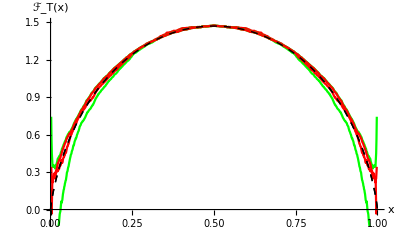

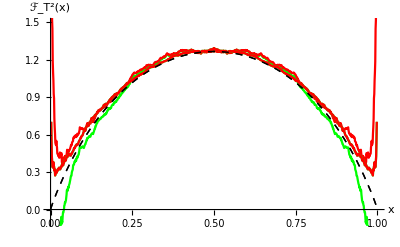

```mathematica
(* show both values of H *)
Show[FT[0.45],FT[0.55]]
Show[FT2[0.45],FT2[0.55]]
```

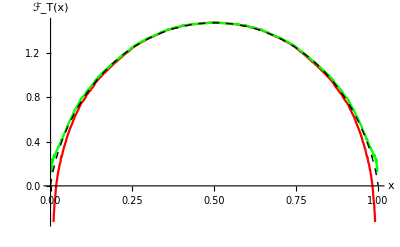

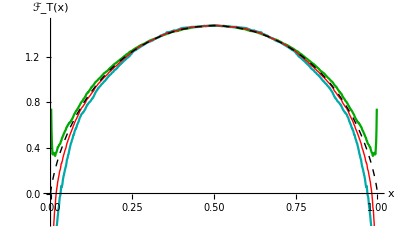

/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT-mean.eps

```mathematica
(* the mean between 0.45 and 0.55 *)
{reddata=(FTdata[0.45]+FTdata[0.55])/2,greendata=(FTdata2[0.45]+FTdata2[0.55])/2};
ListLinePlot[%,PlotStyle->{Red,Green}];
Plot[((oneloopT)),{x,0,1},PlotStyle->{Thick,Black,Dashed}];
PP1=Show[%%,%,AxesLabel->{x,Subscript[ℱ, T][x]}]
reddata=reddata/.{a_,b_}->{a,b}+{0,0 0.025};
ListLinePlot[FTdata[0.45],PlotStyle->color[0.45]];
ListLinePlot[FTdata[0.55],PlotStyle->color[0.55]];
ListLinePlot[reddata,PlotStyle->color[0.5]];
Plot[oneloopT,{x,0,1},PlotStyle->{Thick,Black,Dashed}];
Show[%%%,%%%%,%%,%,AxesLabel->{x,Subscript[ℱ, T][x]},PlotRange->{-.25,1.5}]

If[export,Export["/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT-mean.eps",%]]
```

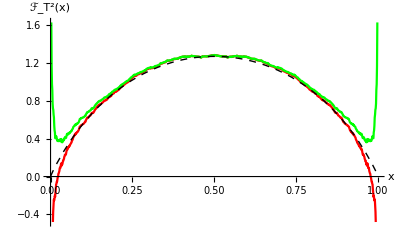

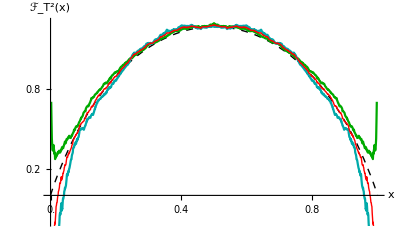

/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT2-mean.eps

```mathematica
(* the mean between 0.45 and 0.55 *)
shift=-0.0;
{reddata=(FT2data[0.45]+FT2data[0.55])/2,greendata=(FT2data2[0.45]+FT2data2[0.55])/2};
reddata=reddata/.{a_,b_}->{a,b+shift};
greendata=greendata/.{a_,b_}->{a,b+shift};
ListLinePlot[{reddata,greendata},PlotStyle->{Red,Green}];
Plot[((fitT2)),{x,0,1},PlotStyle->{Thick,Black,Dashed}];
PP2=Show[%%,%,AxesLabel->{x,Subscript[ℱ, T^2][x]}]
ListLinePlot[FT2data[0.45],PlotStyle->color[0.45]];
ListLinePlot[FT2data[0.55],PlotStyle->color[0.55]];
ListLinePlot[reddata,PlotStyle->color[0.5]];
Plot[fitT2,{x,0,1},PlotStyle->{Thick,Black,Dashed}];
Show[%,%%%,%%%%,%%,AxesLabel->{x,Subscript[ℱ, T^2][x]},PlotRange->{-.2,1.3},Ticks->{Table[i,{i,0,1,0.2}],Table[i,{i,-1,2,0.2}]}]
If[export,Export["/Users/wiese/Dropbox/tex/persistence/2absorbingboundaries/figures/FT2-mean.eps",%]]
```

F-T

H=0.45:

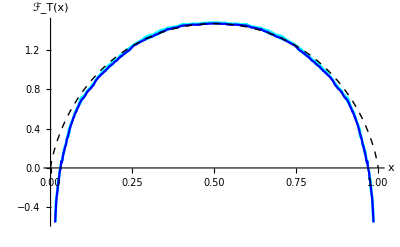

H=0.55:

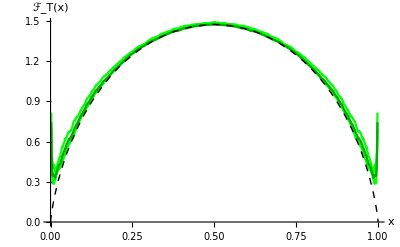

mean of H=0.45 and H=0.55:

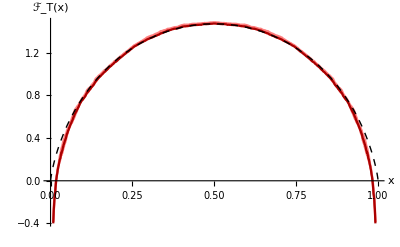

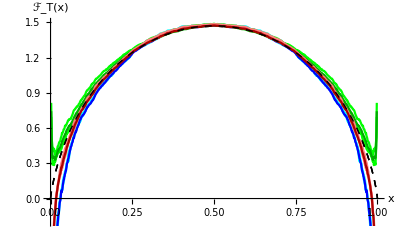

```mathematica
Print["F-T"]
(* in blue 0.45 *)
Print["H=0.45:"]
ListLinePlot[FTdata[0.45],PlotStyle->Blue,AxesLabel->{x,Subscript[ℱ, T][x]}];
ListLinePlot[FTdataUnsymp[0.45],PlotStyle->Cyan,AxesLabel->{x,Subscript[ℱ, T][x]}];
ListLinePlot[{Transpose[FTdataUnsymp[0.45]][[1]],Transpose[FTdataUnsymp[0.45]][[2]]//Reverse}//Transpose,PlotStyle->Cyan,AxesLabel->{x,Subscript[ℱ, T][x]}];
PS1={%,%%,%%%,Plot[fitT,{x,0,1},PlotStyle->{Thick,Black,Dashed},AxesLabel->{x,Subscript[ℱ, T][x]}]}//Show
(* in gree 0.55 *)
Print["H=0.55:"]
ListLinePlot[FTdata[0.55],PlotStyle->Darker[Green]];
ListLinePlot[FTdataUnsymp[0.55],PlotStyle->Green];
ListLinePlot[{Transpose[FTdataUnsymp[0.55]][[1]],Transpose[FTdataUnsymp[0.55]][[2]]//Reverse}//Transpose,PlotStyle->Green,AxesLabel->{x,Subscript[ℱ, T][x]}];
PS2={%,%%,%%%,Plot[fitT,{x,0,1},PlotStyle->{Thick,Black,Dashed}]}//Show
(* in red the mean *)
Print["mean of H=0.45 and H=0.55:"]
ListLinePlot[(FTdata[0.45]+FTdata[0.55])/2,PlotStyle->Darker[Red]];
ListLinePlot[(FTdataUnsymp[0.45]+FTdataUnsymp[0.55])/2,PlotStyle->Pink];
ListLinePlot[{Transpose[FTdataUnsymp[0.45]][[1]],(Transpose[FTdataUnsymp[0.45]][[2]]+Transpose[FTdataUnsymp[0.55]][[2]])/2//Reverse}//Transpose,PlotStyle->Pink,AxesLabel->{x,Subscript[ℱ, T][x]}];
PS3={%,%%,%%%,Plot[fitT,{x,0,1},PlotStyle->{Thick,Black,Dashed}]}//Show
Show[PS1,PS2,PS3,PlotRange->{-.2,1.5}]
```

H=0.45:

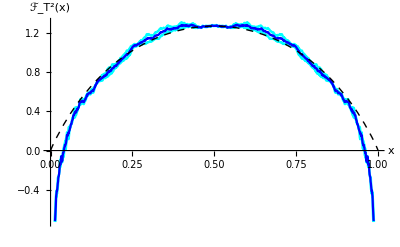

H=0.55:

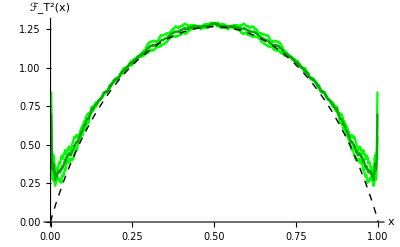

mean of H=0.45 and H=0.55:

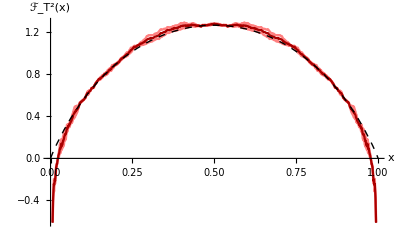

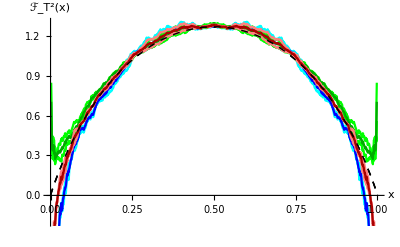

```mathematica
(* in blue 0.45 *)
Print["H=0.45:"]
ListLinePlot[FT2data[0.45],PlotStyle->Blue];
ListLinePlot[FT2dataUnsymp[0.45],PlotStyle->Cyan];
ListLinePlot[{Transpose[FT2dataUnsymp[0.45]][[1]],Transpose[FT2dataUnsymp[0.45]][[2]]//Reverse}//Transpose,PlotStyle->Cyan,AxesLabel->{x,Subscript[ℱ, T^2][x]}];
PS1={%,%%,%%%,Plot[fitT2,{x,0,1},PlotStyle->{Thick,Black,Dashed}]}//Show
(* in gree 0.55 *)
Print["H=0.55:"]
ListLinePlot[FT2data[0.55],PlotStyle->Darker[Green]];
ListLinePlot[FT2dataUnsymp[0.55],PlotStyle->Green];
ListLinePlot[{Transpose[FT2dataUnsymp[0.55]][[1]],Transpose[FT2dataUnsymp[0.55]][[2]]//Reverse}//Transpose,PlotStyle->Green,AxesLabel->{x,Subscript[ℱ, T^2][x]}];
PS2={%,%%,%%%,Plot[fitT2,{x,0,1},PlotStyle->{Thick,Black,Dashed}]}//Show
(* in red the mean *)
Print["mean of H=0.45 and H=0.55:"]
ListLinePlot[(FT2data[0.45]+FT2data[0.55])/2,PlotStyle->{Darker[Red]}];
ListLinePlot[(FT2dataUnsymp[0.45]+FT2dataUnsymp[0.55])/2,PlotStyle->Pink];
ListLinePlot[{Transpose[FT2dataUnsymp[0.45]][[1]],(Transpose[FT2dataUnsymp[0.45]][[2]]+Transpose[FT2dataUnsymp[0.55]][[2]])/2//Reverse}//Transpose,PlotStyle->Pink,AxesLabel->{x,Subscript[ℱ, T^2][x]}];
PS3={%,%%,%%%,Plot[fitT2,{x,0,1},PlotStyle->{Thick,Black,Dashed}]}//Show
Show[PS1,PS2,PS3,PlotRange->{-.2,1.3}]
```

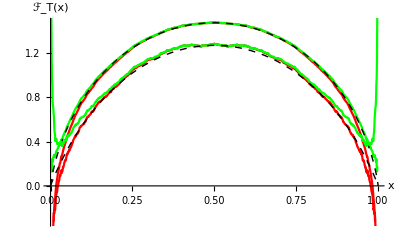

```mathematica
Show[PP1,PP2]
```

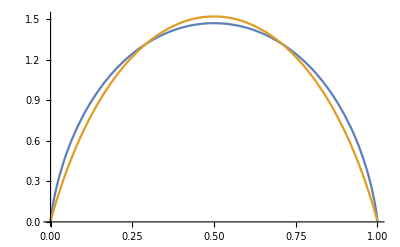

```mathematica
Plot[{((oneloopT)),1.2((fitT2))},{x,0,1}]
```